# Practical 1

## Aim : - a) Solution of Cauchy problem for first order PDE. b) Plotting the characteristics for the first order PDE. c) Plot the integral surface of a given first order PDE with initial data.

```mathematica
pde1 = D[u[x,y],x]+x*D[u[x,y],y]==0;
c1 = u[0,y]==Sin[y];
sol1 = DSolve[{pde1,c1},u[x,y],{x,y}]
```

{{u[x,y]→Sin[1/2 (-x^2+2 y)]}}

```mathematica
(* Characteristic Plot *)
```

```mathematica
ch =  DSolve[{D[y[x],x]== x},y[x],x]/.{C[1]->1}
```

{{y[x]→1+x^2/2}}

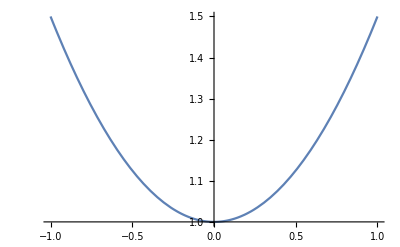

```mathematica
Plot[y[x]/.ch,{x,-1,1}]
```

```mathematica
Plot3D[u[x,y]/.sol1,{x,-4,4},{y,-4,4}]
```

-Graphics3D-

```mathematica
ClearAll;
```

{{u[x,y]→(2 x^3+x^4 y-y^3)/x^3}}

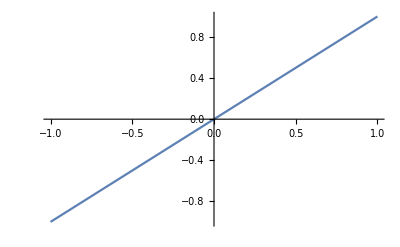

-Graphics3D-

```mathematica
pde2 = x*D[u[x,y],x]+y*D[u[x,y],y]==2x*y;
c2 = u[x,x^2]==2;
sol2 = DSolve[{pde2,c2},u[x,y],{x,y}]
ch2 =  DSolve[{D[y[x],x]== y[x]/x},y[x],x]/.{C[1]->1};
Plot[y[x]/.ch2,{x,-1,1}]
Plot3D[u[x,y]/.sol2,{x,-4,4},{y,-4,4}]
```

```mathematica
ClearAll;
```

{{u[x,t]→ⅇ^(-x^2/t^6)}}

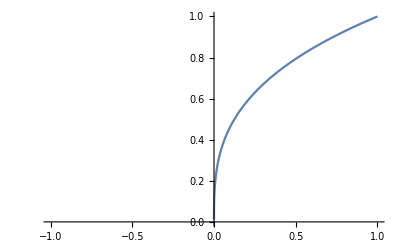

-Graphics3D-

```mathematica
pde3 = 3*x*D[u[x,t],x]+t*D[u[x,t],t]==0;
c3 = u[x,1]==Exp[-x^2];
sol3 = DSolve[{pde3,c3},u[x,t],{x,t}]
ch3 =  DSolve[{D[t[x],x]== t[x]/(3x)},t[x],x]/.{C[1]->1};
Plot[t[x]/.ch3,{x,-1,1}]
Plot3D[u[x,t]/.sol3,{x,-4,4},{t,-4,4}]
```